# Practical 7

### Submitted By- Puranjyoti Bera (20201043)

Make a plot of the vertical lines x = a for a = -1, -1/2, 1/2, 1 and the horizontal lines y = b for b = -1, -1/2, 1/2, 1. Find the plot of the grid under the mapping w = f(z) = 1/z.

The vertical lines x = 1, -1/2, 1/2, 1 and the horizontal lines y = 1, -1/2, 1/2, 1 are given by the figure

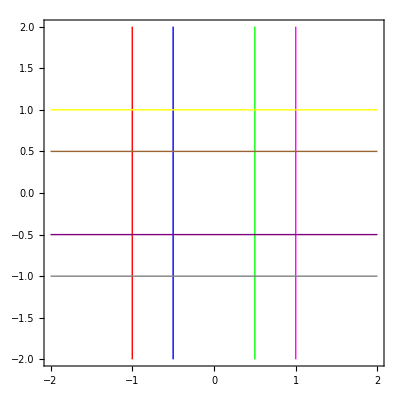

The image of the verticl lines x = 1, -1/2, 1/2, 1 and the horizontal lines y = 1, -1/2, 1/2, 1 under the function f(z)=1/z is given by the figure

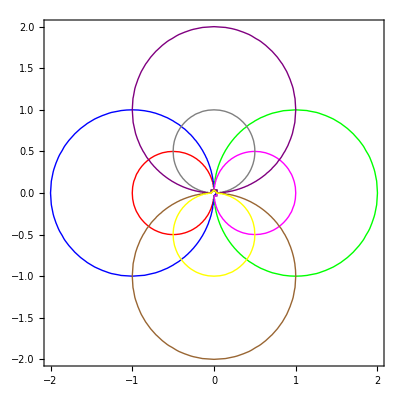

```mathematica
Print["The vertical lines x = 1, -1/2, 1/2, 1 and the horizontal lines y = 1, -1/2, 1/2, 1 are given by the figure"];
grid:={-1,-1/2,1/2,1};
xcolour:={Red,Blue,Green,Magenta};
ycolour:={Gray,Purple,Brown,Yellow};
Show[Table[ContourPlot[Re[x+I*y]==grid[[i]],{x,-2,2},{y,-2,2},ContourStyle->{Thick,xcolour[[i]]},Axes->True],{i,1,4}],Table[ContourPlot[Im[x+I*y]==grid[[i]],{x,-2,2},{y,-2,2},ContourStyle->{Thick,ycolour[[i]]},Axes->True],{i,1,4}]]
f[z_]:=1/z;
w=u+I*v;
root:=z/.ComplexExpand[Solve[f[z]==w,z]];
Print["The image of the verticl lines x = 1, -1/2, 1/2, 1 and the horizontal lines y = 1, -1/2, 1/2, 1 under the function f(z)=",f[z], " is given by the figure"];
Show[Table[ContourPlot[Re[root[[1]]]==grid[[i]],{u,-2,2},{v,-2,2},ContourStyle->{Thick,xcolour[[i]]},Axes->True],{i,1,4}],Table[ContourPlot[Im[root[[1]]]==grid[[i]],{u,-2,2},{v,-2,2},ContourStyle->{Thick,ycolour[[i]]},Axes->True],{i,1,4}]]
```